## Import application packages

```mathematica
<<ProbabilisticBricks`
```

## Block’s aspect ratio b/h>>2 μ_s

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[100,60,3,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,2,0,0,0},{nelx}];
p[[5;;7]]={0,0,20,20,0,0};
p[[30;;32]]={0,0,20,20,0,0};
p[[55;;57]]={0,0,20,20,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

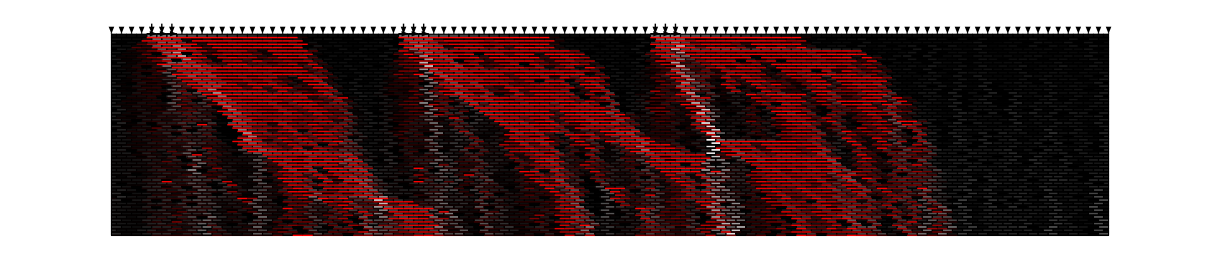

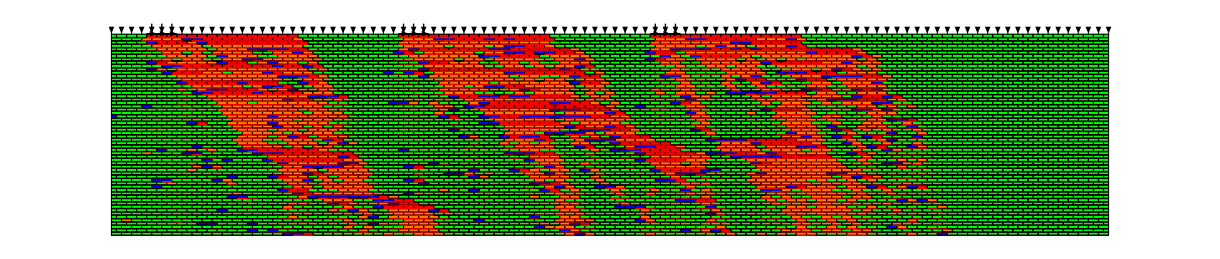

```mathematica
solveProblem[];
dwg1=displayWallWithFilter["stress_state"]
dwg2=displayWallWithFilter["contacts_state"]
```

### Export graphics

```mathematica
Export["risultati_carichi_h_bh_alto_ss.pdf",dwg1,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_bh_alto_ss.pdf

```mathematica
Export["risultati_carichi_h_bh_alto_cs.pdf",dwg2,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_bh_alto_cs.pdf

## Block’s aspect ratio b/h>2 μ_s

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[100,60,2,1,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,2,0,0,0},{nelx}];
p[[5;;7]]={0,0,20,20,0,0};
p[[30;;32]]={0,0,20,20,0,0};
p[[55;;57]]={0,0,20,20,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

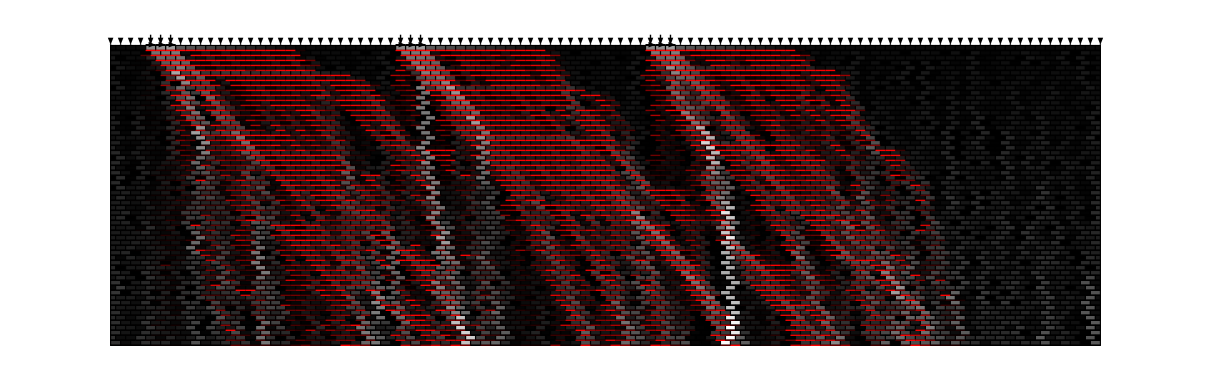

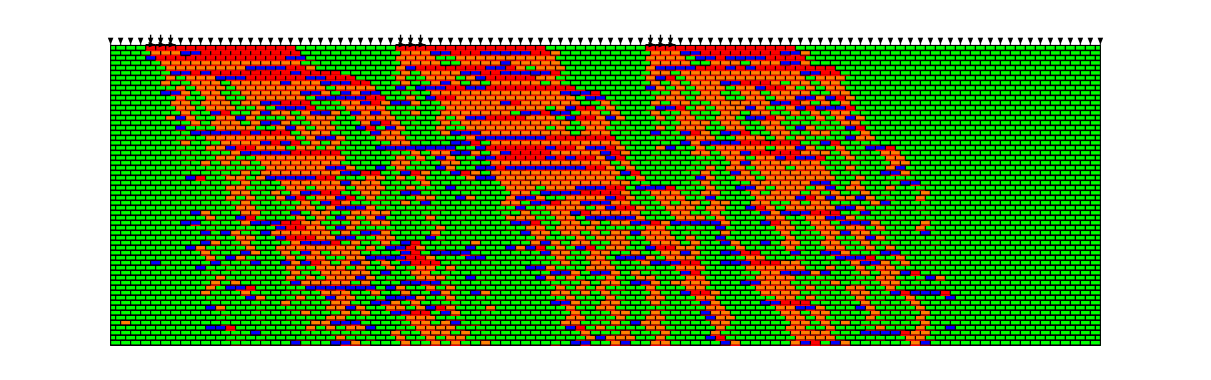

```mathematica
solveProblem[];
dwg3=displayWallWithFilter["stress_state"]
dwg4=displayWallWithFilter["contacts_state"]
```

### Export graphics

```mathematica
Export["risultati_carichi_h_bh_medio_ss.pdf",dwg3,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_bh_medio_ss.pdf

```mathematica
Export["risultati_carichi_h_bh_medio_cs.pdf",dwg4,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_bh_medio_cs.pdf

## Block’s aspect ratio b/h<2 μ_s

### Problem initialization

Set the geometry and other parameters using setProblemProperties[nelx, nely, b, h, P, μ], where nelx is the number of bricks per course, nely the number of courses, b and h are the dimensions of the brick, P is the weight of a brick and μ the static friction coefficient

```mathematica
setProblemProperties[100,60,2,1.5,0.1,0.7];
```

Generate random contacts

```mathematica
generateContacts[];
```

### Boundary conditions - Loads

Initialize the vector of loads acting on top of the wall in the form of {... N_1,V_1,N_2,V_2,N_3,V_3...} where every group of six components represents the loads on a brick ordered from left to right

```mathematica
p=Table[{0,0,2,0,0,0},{nelx}];
p[[5;;7]]={0,0,20,20,0,0};
p[[30;;32]]={0,0,20,20,0,0};
p[[55;;57]]={0,0,20,20,0,0};
p=Flatten[p];
setBoundaryConditions[p];
```

### Solution

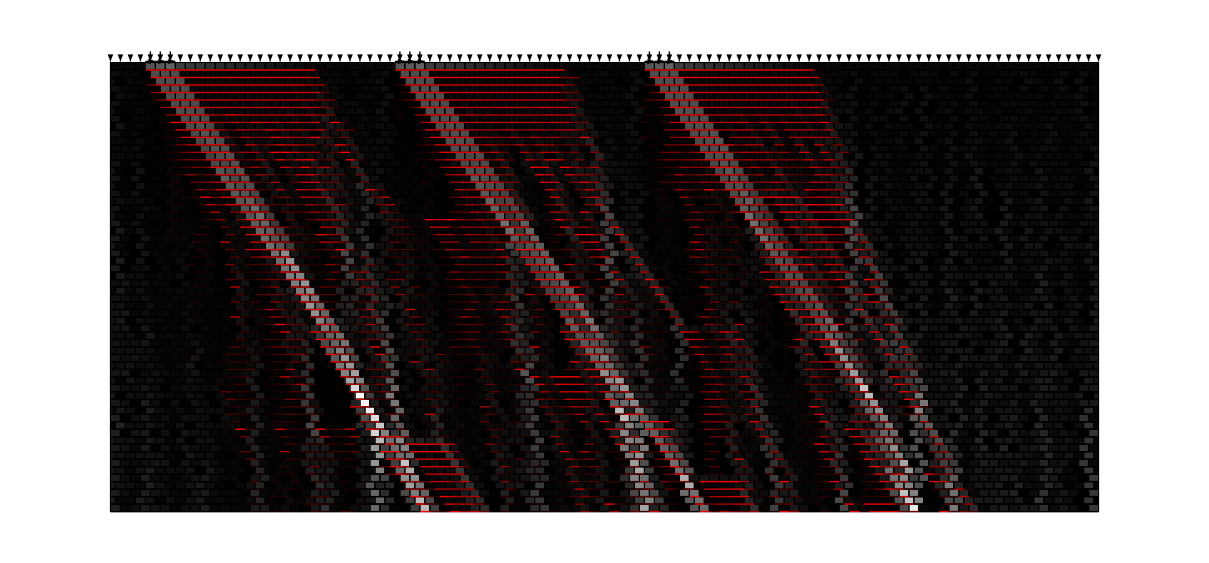

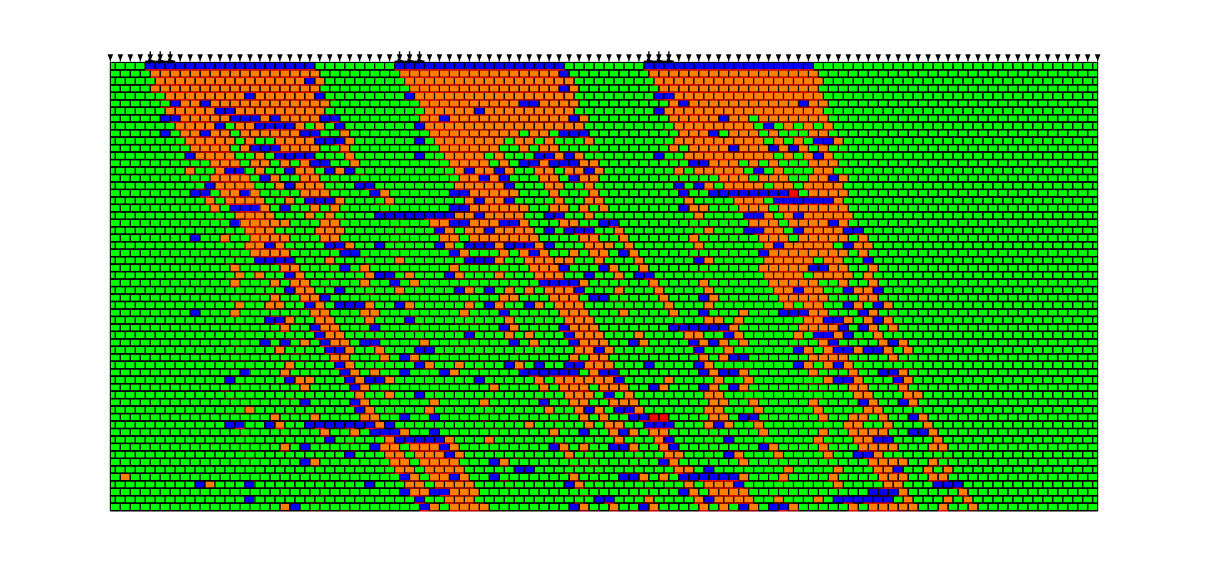

```mathematica
solveProblem[];
dwg5=displayWallWithFilter["stress_state"]
dwg6=displayWallWithFilter["contacts_state"]
```

### Export graphics

```mathematica
Export["risultati_carichi_h_bh_basso_ss.pdf",dwg5,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_bh_basso_ss.pdf

```mathematica
Export["risultati_carichi_h_bh_basso_cs.pdf",dwg6,ImageSize->1000,ImageResolution->200]
```

risultati_carichi_h_bh_basso_cs.pdf